## Snake Coordinates

```mathematica
ClearAll["Global`*"]
```

Define the Minkowski metric.

```mathematica
η={{-1,0,0,0},{0,1,0,0},{0,0,1,0},{0,0,0,1}};
MatrixForm[η]
```

(-1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | 1)

Define the snake coordinates.

```mathematica
snakerule={tp->t,xp->x-a Sin[k y],yp->y,zp->z};
```

Define rule to translate between coordinate systems.

```mathematica
unsnakerule=Quiet@FullSimplify@Normal[Solve[{tp==(tp/.snakerule),xp==(xp/.snakerule),
                                             yp==(yp/.snakerule),zp==(zp/.snakerule)},{t,x,y,z}]][[1]];
```

Define two different coordinate systems.

```mathematica
mup={tp,xp,yp,zp};
mu={t,x,y,z};
```

Find the metric in snake coordinates.

```mathematica
J=FullSimplify[Table[D[mu[[i]]/.unsnakerule,mup[[j]]],{i,1,4},{j,1,4}]];
Ji=FullSimplify[Table[D[mup[[i]]/.snakerule,mu[[j]]],{i,1,4},{j,1,4}]];
gcov=FullSimplify[Table[Sum[J[[m,mp]]*J[[n,np]]*η[[m,n]],{m,1,4},{n,1,4}],{mp,1,4},{np,1,4}]/.xp->x];
gcon=FullSimplify[Inverse[gcov]];
"g" ->MatrixForm[gcov]
"gi"->MatrixForm[gcon]
```

g→(-1 | 0 | 0 | 0
0 | 1 | a k Cos[k yp] | 0
0 | a k Cos[k yp] | 1+a^2 k^2 Cos[k yp]^2 | 0
0 | 0 | 0 | 1)

gi→(-1 | 0 | 0 | 0
0 | 1+a^2 k^2 Cos[k yp]^2 | -a k Cos[k yp] | 0
0 | -a k Cos[k yp] | 1 | 0
0 | 0 | 0 | 1)

Derivatives of the metric.

```mathematica
dgdy=FullSimplify[D[gcov,yp]];
"dgdy"->MatrixForm[dgdy]
```

dgdy→(0 | 0 | 0 | 0
0 | 0 | -a k^2 Sin[k yp] | 0
0 | -a k^2 Sin[k yp] | -a^2 k^3 Sin[2 k yp] | 0
0 | 0 | 0 | 0)

```mathematica
FullSimplify[Sqrt[-Det[gcov]]]
```

1

#### Gram-Schmidt

```mathematica
f0=1; f1=2; f2=3; f3=4;
t1=1; t2=2; t3=3;
```

```mathematica
α=(-gcon[[f0,f0]])^(-1/2);
γcov=Table[gcov[[i,j]],{i,f1,f3},{j,f1,f3}];
γcon=α^2 Table[(gcon[[f0,i]]*gcon[[f0,j]]-gcon[[f0,f0]]*gcon[[i,j]]),{i,f1,f3},{j,f1,f3}];
```

```mathematica
xμ={xp,yp,zp};
q={xp+a Sin[k yp],yp,zp};
```

```mathematica
A3[j_]:=Table[D[q[[t3]],xμ[[n]]],{n,t1,t3}][[j]];
matA3=FullSimplify@Table[Sum[γcon[[i,j]]*A3[j],{j,t1,t3}],{i,t1,t3}];
matB3=FullSimplify@matA3;
matC3=FullSimplify@Table[Sum[γcov[[j,k]]*matB3[[j]]*matB3[[k]],{j,t1,t3},{k,t1,t3}]^(-1/2)matB3[[i]],{i,t1,t3}];
matC3=FullSimplify[FullSimplify[matC3]];
```

```mathematica
A1[j_]:=Table[D[q[[t1]],xμ[[n]]],{n,t1,t3}][[j]];
matA1=FullSimplify@Table[Sum[γcon[[i,j]]*A1[j],{j,t1,t3}],{i,t1,t3}];

matB1=FullSimplify@Table[matA1[[i]]-Sum[γcov[[j,k]]*matA1[[j]]*matC3[[k]]*matC3[[i]],{j,t1,t3},{k,t1,t3}],{i,t1,t3}];
matB1=FullSimplify[matB1];
matC1=Table[Sum[γcov[[j,k]]*matB1[[j]]*matB1[[k]],{j,t1,t3},{k,t1,t3}]^(-1/2)matB1[[i]],{i,t1,t3}];
matC1=FullSimplify[matC1];
```

```mathematica
A2[j_]:=Table[D[q[[t2]],xμ[[n]]],{n,t1,t3}][[j]];
matA2=FullSimplify@Table[Sum[γcon[[i,j]]*A2[j],{j,t1,t3}],{i,t1,t3}];
matB2=Table[(matA2[[i]]
             -Sum[γcov[[j,k]]*matA2[[j]]*matC3[[k]]*matC3[[i]],{j,t1,t3},{k,t1,t3}]
             -Sum[γcov[[j,k]]*matA2[[j]]*matC1[[k]]*matC1[[i]],{j,t1,t3},{k,t1,t3}]),{i,t1,t3}];
matB2=FullSimplify[matB2];
matC2=Table[Sum[γcov[[j,k]]*matB2[[j]]*matB2[[k]],{j,t1,t3},{k,t1,t3}]^(-1/2)matB2[[i]],{i,t1,t3}];
matC2=matC2;
```

```mathematica
matC0=Table[-α gcon[[f0,μ]],{μ,f0,f3}];
```

```mathematica
tetrad=Assuming[a>0&&k>0,
                FullSimplify[{matC0,
                              Prepend[matC1,0],
                              Prepend[matC2,0],
                              Prepend[matC3,0]}]];
```

Here is the Cartesian tetrad for Snake coordinates:

```mathematica
MatrixForm@tetrad
```

(1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | -a k Cos[k yp] | 1 | 0
0 | 0 | 0 | 1)

In the limit of a → 0, the tetrad should approach the identity matrix.

```mathematica
MatrixForm[Limit[tetrad,a->0]]
```

(1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | 1)

```mathematica
dtetraddx=Assuming[a>0&&k>0,FullSimplify[D[tetrad,xp]]];
dtetraddy=Assuming[a>0&&k>0,FullSimplify[D[tetrad,yp]]];
dtetraddz=Assuming[a>0&&k>0,FullSimplify[D[tetrad,zp]]];
```

```mathematica
MatrixForm@dtetraddy
```

(0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | a k^2 Sin[k yp] | 0 | 0
0 | 0 | 0 | 0)

The derivatives of the tetrad should go to zero in the limit of M → 0.

```mathematica
MatrixForm[
Limit[dtetraddx,a->0]]
```

(0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0)

## Results

```mathematica
SetDirectory[NotebookDirectory[]];
```

#### Snake Coordinates

```mathematica
mya=0.1;
mym=2.0;
dir=Normalize[D[{x-a Sin[m π y],y,z},y]/.{y->0,a->mya,m->mym}];
y[x_]:=If[Tan[Quantity[85, "AngularDegrees"]](x-0.05)>0&&x>=0, 
          Tan[Quantity[85, "AngularDegrees"]](x-0.05), 
          If[-Tan[Quantity[85, "AngularDegrees"]](x+0.05)>0&&x<=0, -Tan[Quantity[85, "AngularDegrees"]](x+0.05)], 0];
```

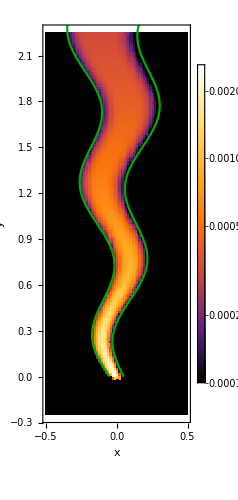

```mathematica
snake=Import["../../build/src/beam_snake.txt","Table"];
snakeplot=
Show[
{ListDensityPlot[Transpose@{snake[[All,1]],snake[[All,2]],snake[[All,3]]/.x_/;x<10^-4->10^-4},
                 InterpolationOrder->0,
                 ColorFunction->"SunsetColors",
                 ScalingFunctions -> {"Linear","Linear","Log10"},
                 PlotRange->{{-0.5,0.5},{-0.25,2.25},{10^-4,10^-2}},
                 PlotRangePadding->None,
                 FrameLabel->{"x","y"},AspectRatio->{1,3},
                 PlotLegends->BarLegend[Automatic,LegendLabel->Placed["R^00", Top],LegendMarkerSize->350]],
 ParametricPlot[{x-mya Sin[mym*π y[x]],y[x]},
                {x,-0.5,0.5},AspectRatio->{1,3},
                PlotRange->{{-0.5,0.5},{-0.25,2.25}},PlotStyle->Darker@Green]}]
Export["../../build/src/beam_snake.pdf",snakeplot,ImageResolution->500];
```

#### Un-Snake Coordinates

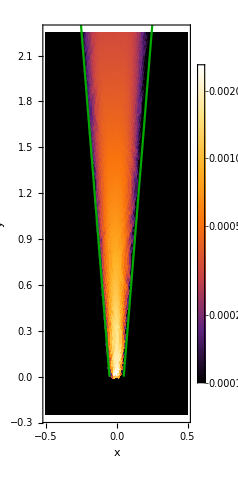

```mathematica
unsnake=Transpose@{snake[[All,1]]+mya Sin[mym π*snake[[All,2]]],snake[[All,2]],snake[[All,3]]/.x_/;x<10^-4->10^-4};
unsnakeplot=
Show[
{ListDensityPlot[Transpose@{unsnake[[All,1]],unsnake[[All,2]],unsnake[[All,3]]/.x_/;x<10^-4->10^-4},
                 InterpolationOrder->0,
                 ColorFunction->"SunsetColors",
                 ScalingFunctions -> {"Linear","Linear","Log10"},
                 PlotRange->{{-0.5,0.5},{-0.25,2.25},{10^-4,10^-2}},
                 PlotRangePadding->None,
                 FrameLabel->{"x","y"},AspectRatio->{1,3},
                 PlotLegends->BarLegend[Automatic,LegendLabel->Placed["R^00", Top],LegendMarkerSize->350]],
 ParametricPlot[{x,y[x]},
                {x,-0.5,0.5},AspectRatio->{1,3},
                PlotRange->{{-0.5,0.5},{-0.25,2.25}},PlotStyle->Darker@Green]}]
Export["../../build/src/beam_unsnake.pdf",unsnakeplot,ImageResolution->500];
```

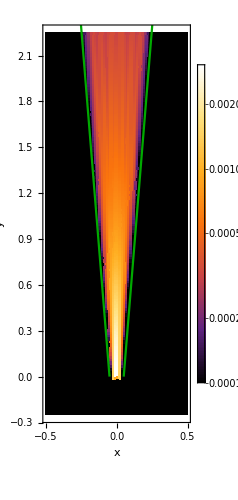

```mathematica
flat=Import["../../build/src/beam_flat.txt","Table"];
flatplot=
Show[
{ListDensityPlot[Transpose@{flat[[All,1]],flat[[All,2]],flat[[All,3]]/.x_/;x<10^-4->10^-4},
                InterpolationOrder->0,
                ColorFunction->"SunsetColors",
                ScalingFunctions -> {"Linear","Linear","Log10"},
                PlotRange->{{-0.5,0.5},{-0.25,2.25},{10^-4,10^-2}},
                PlotRangePadding->None,
                FrameLabel->{"x","y"},AspectRatio->{1,3},
                PlotLegends->BarLegend[Automatic,LegendLabel->Placed["R^00", Top],LegendMarkerSize->350]],
 ParametricPlot[{x,y[x]},
                {x,-0.5,0.5},AspectRatio->{1,3},
                PlotRange->{{-0.5,0.5},{-0.25,2.25}},PlotStyle->Darker@Green]}]
Export["../../build/src/beam_flat.pdf",flatplot,ImageResolution->500];
```